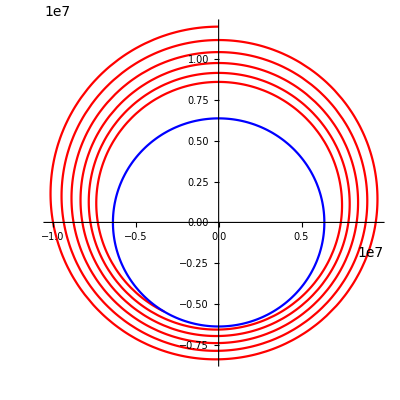

-Graphics-

```mathematica
G = 6.67 10^-11 ;                                 (*gravitational constant*)
M = 5.97219×10^24 ;                            (*mass of earth in kilograms*)
r0 =12000  10^3 ;                              (*initial distance of the satellite from the centre of the Earth in metres*) 
v0KmpHr = 19000;                               (*initial speed of the satellite in km/hr fired horizontally*) 
v0Mps  = v0KmpHr 5/18 ;                      (*initial speed of the satellite in m/s fired horizontally*) 
phid0 = v0Mps/r0;   
RE = 6378 1000 ;                              (*radius of the Earth*)
airDrag =34 ;                                      (*amount of air drag*)
tFin = 140000 ;                                  (*how much time is to be simulated*)

StopCriterion =      {WhenEvent[  { r[t]  < RE || t >tFin}   ,end=t;"StopIntegration"] } ;     
sol=NDSolve[{r[t] phi''[t]+ 2 r'[t]phi'[t] ==0 -airDrag  phi'[t]   ,r''[t] - r[t] phi'[t]^2   == (- (G M ))/r[t]^2       ,r[0]==r0, phi[0]==π/2 ,r'[0]==0, phi'[0]== phid0, StopCriterion},{r,phi},{t,∞}] //Quiet    ;

p1 =ParametricPlot[Evaluate[{r[t] Cos[phi[t]], r[t] Sin[phi[t]]}/. sol],{t,0,end}, AspectRatio->1, PlotStyle->Red,PlotRange->Full]  ;
p2 =ParametricPlot[{ RE Cos[u],RE Sin[u]},{u,0,2 Pi}, PlotStyle->Blue, PlotRange->Full]  ;
Show[p1,p2]
Show[p1,p2, PlotRange->All]
```